```mathematica
a1=({{0, 1, 0}, {1, 0, 0}, {0, 0, 0}});a2=({{0, -I, 0}, {I, 0, 0}, {0, 0, 0}});a3=({{1, 0, 0}, {0, -1, 0}, {0, 0, 0}});a4=({{0, 0, 1}, {0, 0, 0}, {1, 0, 0}});a5=({{0, 0, -I}, {0, 0, 0}, {I, 0, 0}});a6=({{0, 0, 0}, {0, 0, 1}, {0, 1, 0}});a7=({{0, 0, 0}, {0, 0, -I}, {0, I, 0}});a8=({{1, 0, 0}, {0, 1, 0}, {0, 0, -2}});
```

```mathematica
b1=({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}});b2=Sqrt[3]/2({{0, 1, 0}, {1, 0, 1}, {0, 1, 0}});b3=(I Sqrt[3])/2({{0, -1, 0}, {1, 0, -1}, {0, 1, 0}});b4=Sqrt[3/2]({{1, 0, 0}, {0, 0, 0}, {0, 0, -1}});b5=(I Sqrt[3/2])({{0, 0, -1}, {0, 0, 0}, {1, 0, 0}});b6=Sqrt[3]/2({{0, 1, 0}, {1, 0, -1}, {0, -1, 0}});b7=(I Sqrt[3])/2({{0, -1, 0}, {1, 0, 1}, {0, -1, 0}});b8=({{-1/2, 0, Sqrt[3]/2}, {0, 1, 0}, {Sqrt[3]/2, 0, -1/2}});
b9=({{-1/2, 0, -Sqrt[3]/2}, {0, 1, 0}, {-Sqrt[3]/2, 0, -1/2}});
```

```mathematica
ψ=1/Sqrt[3]({{1,0,0,0,1,0,0,0,1}})
```

{{1/(√3),0,0,0,1/(√3),0,0,0,1/(√3)}}

```mathematica
psy=ConjugateTranspose[ψ]
```

{{1/(√3)},{0},{0},{0},{1/(√3)},{0},{0},{0},{1/(√3)}}

```mathematica
ρ0=({{1/3, 0, 0, 0, 1/3, 0, 0, 0, 1/3}, {0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0}, {1/3, 0, 0, 0, 1/3, 0, 0, 0, 1/3}, {0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0}, {1/3, 0, 0, 0, 1/3, 0, 0, 0, 1/3}});
```

```mathematica
ρ1=({{0.017330721, 0.043679589, -0.0011132286, -0.0062443004, -0.011850015, 0.004707436, 0.0082768265, 0.036699202, 0.047776532}, {0.043679589, 0.2166103, -0.010740962, -0.01848621, -0.059021694, 0.0021608827, -0.00055448136, -0.0082768267, 0.22767512}, {-0.0011132286, -0.010740962, 0.22392077, -0.0082203424, -0.036055083, -0.063071761, -0.0035817407, 0.0019436425, -1.5276894*^-10}, {-0.0062443004, -0.01848621, -0.0082203424, 0.0027879748, 0.0070857538, 0.0011132286, -0.0014291871, -0.010862555, -0.020566862}, {-0.011850015, -0.059021694, -0.036055083, 0.0070857538, 0.025199544, 0.010740962, 0.0046213262, 0.0014291871, -0.0646114}, {0.004707436, 0.0021608827, -0.063071761, 0.0011132286, 0.010740962, 0.024891396, 0.0019436426, 0.0035817407, 4.7530878*^-11}, {0.0082768265, -0.00055448136, -0.0035817407, -0.0014291871, 0.0046213262, 0.0019436426, 0.017287122, 0.049058619, -2.1801737*^-11}, {0.036699202, -0.0082768267, 0.0019436425, -0.010862555, 0.0014291871, 0.0035817407, 0.049058619, 0.23152504, -1.5776298*^-10}, {0.047776532, 0.22767512, -1.5276894*^-10, -0.020566862, -0.0646114, 4.7530878*^-11, -2.1801737*^-11, -1.5776298*^-10, 0.24044714}});
```

```mathematica
Eigenvalues[ρ0]
```

{1,0,0,0,0,0,0,0,0}

```mathematica
I3=IdentityMatrix[3];
```

```mathematica
A=({{2, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 2, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 2, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 2, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, -2}});
```

```mathematica
H=({{1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, -1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, -1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, -1}});
```

```mathematica
noisychannel3[rhotmp_]:=FullSimplify[(1-2P/3)rhotmp+P/8(KroneckerProduct[a1,I3].rhotmp.KroneckerProduct[a1,I3]+KroneckerProduct[a2,I3].rhotmp.KroneckerProduct[a2,I3]+KroneckerProduct[a3,I3].rhotmp.KroneckerProduct[a3,I3]+KroneckerProduct[a4,I3].rhotmp.KroneckerProduct[a4,I3]+KroneckerProduct[a5,I3].rhotmp.KroneckerProduct[a5,I3]+KroneckerProduct[a6,I3].rhotmp.KroneckerProduct[a6,I3]+KroneckerProduct[a7,I3].rhotmp.KroneckerProduct[a7,I3]+KroneckerProduct[a8,I3].rhotmp.KroneckerProduct[a8,I3])]
```

```mathematica
noisychannel2[rhotmp_]:=FullSimplify[(1-P)rhotmp+P/6(KroneckerProduct[b2,I3].rhotmp.KroneckerProduct[b2,I3]+KroneckerProduct[b3,I3].rhotmp.KroneckerProduct[b3,I3]+KroneckerProduct[b4,I3].rhotmp.KroneckerProduct[b4,I3]+KroneckerProduct[b7,I3].rhotmp.KroneckerProduct[b7,I3]+KroneckerProduct[b6,I3].rhotmp.KroneckerProduct[b6,I3]+KroneckerProduct[b5,I3].rhotmp.KroneckerProduct[b5,I3]+KroneckerProduct[b8,I3].rhotmp.KroneckerProduct[b8,I3]+KroneckerProduct[b9,I3].rhotmp.KroneckerProduct[b9,I3])]
```

```mathematica
noisychannel4[rhotmp_]:=FullSimplify[(1-P)rhotmp+P/6(KroneckerProduct[I3,b2].rhotmp.KroneckerProduct[I3,b2]+KroneckerProduct[I3,b3].rhotmp.KroneckerProduct[I3,b3]+KroneckerProduct[I3,b4].rhotmp.KroneckerProduct[I3,b4]+KroneckerProduct[I3,b7].rhotmp.KroneckerProduct[I3,b7]+KroneckerProduct[I3,b6].rhotmp.KroneckerProduct[I3,b6]+KroneckerProduct[I3,b5].rhotmp.KroneckerProduct[I3,b5]+KroneckerProduct[I3,b8].rhotmp.KroneckerProduct[I3,b8]+KroneckerProduct[I3,b9].rhotmp.KroneckerProduct[I3,b9])]
noisychannel5[rhotmp_]:=FullSimplify[(1-2P/3)rhotmp+P/8(KroneckerProduct[I3,a1].rhotmp.KroneckerProduct[I3,a1]+KroneckerProduct[I3,a2].rhotmp.KroneckerProduct[I3,a2]+KroneckerProduct[I3,a3].rhotmp.KroneckerProduct[I3,a3]+KroneckerProduct[I3,a4].rhotmp.KroneckerProduct[I3,a4]+KroneckerProduct[I3,a5].rhotmp.KroneckerProduct[I3,a5]+KroneckerProduct[I3,a6].rhotmp.KroneckerProduct[I3,a6]+KroneckerProduct[I3,a7].rhotmp.KroneckerProduct[I3,a7]+KroneckerProduct[I3,a8].rhotmp.KroneckerProduct[I3,a8])]
```

```mathematica
noisychannel6[rhotmp_]:=FullSimplify[(1-P)rhotmp+P (KroneckerProduct[I3,I3]/9)]
```

```mathematica
FisherInformation[rhotmp_]:= Module[{lstmp, vec1tmp,vec2tmp,vec3tmp,vec4tmp,var1, i,j},
lstmp=Eigensystem [rhotmp];
vec1tmp=lstmp[[1]];
vec2tmp=lstmp[[2]];
vec3tmp= FullSimplify[Map[Norm,vec2tmp]];
vec4tmp=vec2tmp/vec3tmp;
vec5tmp=Table[Transpose[{vec4tmp[[i]]}],{i,1,Length[vec4tmp]}];
var1=FullSimplify[ 
2 FullSimplify[ Sum[If[vec1tmp[[i]]+vec1tmp[[j]] ==0  ,0 ,2 (FullSimplify[Abs[((vec1tmp[[i]]-vec1tmp[[j]]))
(FullSimplify[Transpose[Conjugate[vec5tmp[[i]]]]].H.
vec5tmp[[j]]) ]][[1,1]]^2)/(vec1tmp[[i]]+vec1tmp[[j]])],{i,1,Length[vec1tmp]},{j,i+1,Length[vec1tmp]}]]
];
Return[var1];
];
```

```mathematica
ρnoise=noisychannel3[ρ0];
```

```mathematica
ρnoise1=noisychannel2[ρ0];
ρnoise2=noisychannel3[ρ1];
ρnoise3=noisychannel2[ρ1];
ρnoise4=noisychannel2[noisychannel4[ρ1]];
ρnoise5=noisychannel2[noisychannel4[ρ0]];
ρnoise6=noisychannel3[noisychannel5[ρ1]];
ρnoise7=noisychannel3[noisychannel5[ρ0]];
ρnoise8=noisychannel6[ρ0];
```

```mathematica
Tr[ρnoise]
```

1/3 (3-2 P)+(2 P)/3

```mathematica
FisherInformationTest[rhotmp_]:= Module[{lstmp, vec1tmp,vec2tmp,vec3tmp,vec4tmp,var1, i,j},
lstmp=Eigensystem [rhotmp];
vec1tmp=Re[lstmp[[1]]];
vec2tmp=lstmp[[2]]; 
$Assumptions=Element[ϕ,Reals];
vec3tmp= FullSimplify[Map[Norm,vec2tmp]];
vec4tmp={};
For[i=1,i≤Length[vec3tmp],i++,
If[N[vec3tmp[[i]]]==0,,AppendTo[vec4tmp,vec2tmp[[i]]/vec3tmp[[i]]]]
];
vec5tmp=Table[Transpose[{vec4tmp[[i]]}],{i,1,Length[vec4tmp]}]; 

var1=FullSimplify[ 
2 FullSimplify[ Sum[If[vec1tmp[[i]]+vec1tmp[[j]] ==0  ,0,2 (FullSimplify[Abs[((vec1tmp[[i]]-vec1tmp[[j]]))
FullSimplify[Transpose[Conjugate[vec5tmp[[i]]]]].A.
vec5tmp[[j]] ]][[1,1]]^2)/(vec1tmp[[i]]+vec1tmp[[j]])],{i,1,Length[vec1tmp]},{j,i+1,Length[vec5tmp]}]]
];
Return[var1];
];
```

# remember the term  [[1,1]]^2

```mathematica
ab1=Table[{p1,FisherInformation[ρnoise/.{P->p1}]},{p1,0,1,0.01}];
```

```mathematica
tab1=Table[{p1,FisherInformation[ρnoise2/.{P->p1}]},{p1,0,1,0.01}];
```

```mathematica
tab2=Table[{p1,FisherInformation[ρnoise1/.{P->p1}]},{p1,0,1,0.01}];
```

#   blue one for max ENT state

#this is for ENT assisted strategy using bipartite qutrit where the optimal state is

```mathematica
table3=Table[{p1,FisherInformation[ρnoise3/.{P->p1}]},{p1,0,1,0.01}];
```

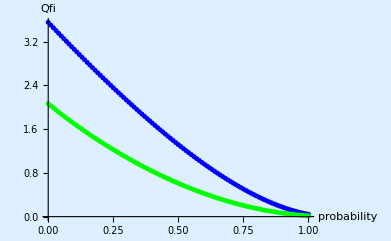

```mathematica
ListPlot[{ab1,tab1},PlotStyle->{Blue,Green, PointSize[0.016]},AxesLabel->{probability , Qfi},Background->LightBlue]
```

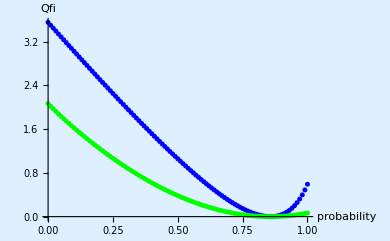

```mathematica
ListPlot[{tab2,table3},PlotStyle->{Blue,Green, PointSize[0.016]},AxesLabel->{probability , Qfi},Background->LightBlue]
```

above two plots are for Ancilla assisted schemes which provide no quantum as for SEP/ classical states QFI=4 so only ENT  assisted strategy provides better precision

below two are ENT assisted strategy

```mathematica
tab3=Table[{p1,FisherInformationTest[ρnoise4/.{P->p1}]},{p1,0,1,0.01}];
```

```mathematica
tab4=Table[{p1,FisherInformationTest[ρnoise5/.{P->p1}]},{p1,0,1,0.01}];
```

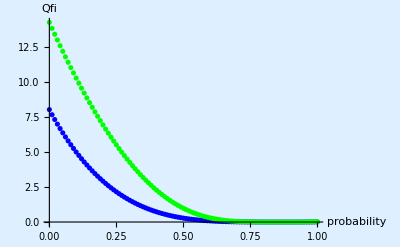

```mathematica
ListPlot[{tab3,tab4},PlotStyle->{Blue,Green, PointSize[0.016]},AxesLabel->{probability , Qfi},Background->LightBlue]
```

```mathematica
tab5=Table[{p1,FisherInformationTest[ρnoise6/.{P->p1}]},{p1,0,1,0.01}];
tab6=Table[{p1,FisherInformationTest[ρnoise7/.{P->p1}]},{p1,0,1,0.01}];
```

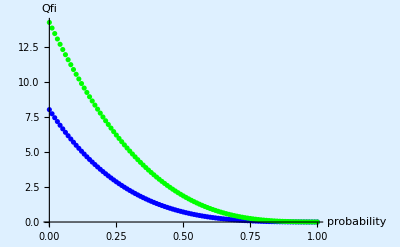

```mathematica
ListPlot[{tab5,tab6},PlotStyle->{Blue,Green, PointSize[0.016]},AxesLabel->{probability , Qfi},Background->LightBlue]
```

```mathematica
tab7=Table[{p1,FisherInformationTest[ρnoise8/.{P->p1}]},{p1,0,1,0.01}];
```

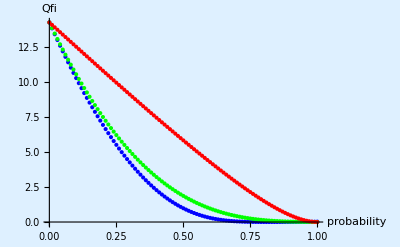

```mathematica
ListPlot[{tab4,tab6,tab7},PlotStyle->{Blue,Green,Red, PointSize[0.016]},AxesLabel->{probability , Qfi},Background->LightBlue]
```